## DPS equation

(25 goldHP)/66

goldAR/20

1/100 (100+bar+iar) (bhp+ihp)

1/100 bhp (100+bar+iar)

1/100 (100+bar) (bhp+ihp)

1/100 (100+bar) (bhp+(25 goldHP)/66)≥1/100 bhp (100+bar+goldAR/20)

1/100 (100+bar) (bhp+(25 x)/66)≥1/100 bhp (100+bar+x/20)

250 (100+bar)≥33 bhp||33 bhp≤25000

757.576

Limit[250 (100+bar)≥33 bhp,bhp→∞]

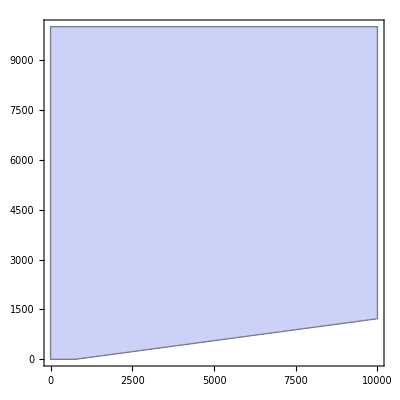

1/100 (100+bar) (bhp+(25 goldHP)/66)==1/100 bhp (100+bar+goldAR/20)

1/100 (100+bar) (bhp+(25 x)/66)==1/100 bhp (100+bar+x/20)

{{bar→ConditionalExpression[-100+(33 bhp)/250,x>0]}}

{{bhp→-25000/33}}

757.576

```mathematica
ghp = (25 goldHP)/66
gar = goldAR/20

ehp = FullSimplify[(bhp+ihp) (mit[bar+iar])]
ehpAR = (bhp) (mit[bar+iar])
ehpHP = (bhp+ihp) (mit[bar])

hmm2 = (ehpHP ≥ ehpAR) /. {ihp -> ghp, iar -> gar}
hmm3 = hmm2 /. {goldAR -> x, goldHP -> x}

LogicalExpand@Assuming[{x>0,bar>0,bhp>0},FullSimplify@Reduce[{hmm3, x>0, bar>0,bhp>0},Reals]]
25000/33.0
Limit[250 (100+bar)≥33 bhp, bhp -> Infinity]
RegionPlot[250 (100+bar)≥33 bhp, {bhp,0,10000}, {bar,0,10000}]

hmm2 = (ehpHP == ehpAR) /. {ihp -> ghp, iar -> gar}
hmm3 = hmm2 /. {goldAR -> x, goldHP -> x}
Solve[{hmm3, x>0}]
Solve[{100+(33 bhp)/250 == 0}, bhp]
25000/33.0
```

```mathematica
mit[d_] := 1/(100/(100+d))
ghp = (25 goldHP)/66
gar = goldAR/20

ehp = FullSimplify[(bhp+ihp) ((mit[bar+iar]*scale) + (mit[bmr+imr]*(1-scale)))]
ehpAR = (bhp) (mit[bar+iar]*scale)
ehpHP = (bhp+ihp) (mit[bar]*scale)
Clear[x,ar,hp,mr,scale]

domain = { ihp ≥ 0, iar ≥ 0, imr ≥ 0, bhp > 0, bar > 0, bmr > 0};
vars = First/@domain;
system2 = Join[domain, {
	ehpHP ≥ ehpAR,
	scale ≥ 0, scale ≤ 1}];

Assuming[{bhp > 0, bar > 0, bmr > 0, ar ≥ 0, hp ≥ 0, mr ≥ 0, scale ≥ 0, scale ≤ 1}, FullSimplify[Reduce[system2, scale, Reals]]];
N@FindInstance[system2, Append[vars,scale], Reals, 4] // TableForm;
hmm2 = (ehpHP ≥ ehpAR) /. {ihp -> ghp, iar -> gar}
hmm3 = hmm2 /. {goldAR -> x, goldHP -> x}
hmm = hmm3 /. (a_ ≥ b_ :> FullSimplify[a] ≥ FullSimplify[b])
FullSimplify[hmm /. {bhp -> 120, bar -> 13}] 
LogicalExpand@Assuming[{scale ≥ 0, scale ≤ 1, bar > 0, bhp > 0, x>0}, FullSimplify@Reduce[{(250 (100+bar)-33 bhp) scale x≥0, bar ≠ 0, bhp ≠ 0}, bhp, Reals]]
```

(25 goldHP)/66

goldAR/20

1/100 (bhp+ihp) (100+bmr+imr+(bar-bmr+iar-imr) scale)

1/100 bhp (100+bar+iar) scale

1/100 (100+bar) (bhp+ihp) scale

1/100 (100+bar) (bhp+(25 goldHP)/66) scale≥1/100 bhp (100+bar+goldAR/20) scale

1/100 (100+bar) scale (bhp+(25 x)/66)≥1/100 bhp scale (100+bar+x/20)

1/100 (100+bar) scale (bhp+(25 x)/66)≥(bhp scale (2000+20 bar+x))/2000

scale x≥0

250 (100+bar)≥33 bhp||scale≤0

```mathematica
constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 3000};
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]
PiecewiseExpand[knownBestDistro]
```

{1/100 (bhp+ihp) (100+bmr+imr+(bar-bmr+iar-imr) scale),{hp→1500,ar→750,mr→750}}

{hp→1500,ar→750,mr→750}

## Path of steepest ascent

```mathematica
g = Grad[ehp /. {hp -> x, ar -> y, mr -> z}, {x,y,z}]
```

{(2000+scale y+z-scale z)/5280,(scale x)/5280,((1-scale) x)/5280}

(-1000+scale C[1]-(-1+scale) x^2 C[2])/scale

(1000+scale C[1])/(-1+scale)+x^2 C[2]

(C[1]|C[2])∈Reals&&((x==0&&C[1]>1000&&scale≥1000/C[1])||(scale>0&&(-1000+scale C[1])/x^2+C[2]≥scale C[2]))

(C[1]|C[2])∈Reals&&((x==0&&C[1]<-1000&&scale+1000/C[1]≥0)||C[2]≥(1000+scale C[1])/x^2+scale C[2])

1/2

{hp→Piecewise[{{3000, 1/3≤scale≤2/3}, {(500 (-5+3 scale))/(-1+scale), 3 scale<1}, {(500 (2+3 scale))/scale, True}}],ar→Piecewise[{{(500 (-2+3 scale))/scale, 3 scale>2}, {0, True}}],mr→Piecewise[{{(500 (-1+3 scale))/(-1+scale), 3 scale<1}, {0, True}}]}

{hp→Piecewise[{{(1000 (-4+3 scale))/(-1+scale), 2 scale≤1}, {1000 (3+1/scale), True}}],ar→Piecewise[{{500, 2 scale==1}, {1000 (3-1/scale), 2 scale>1}, {0, True}}],mr→Piecewise[{{500, 2 scale==1}, {1000 (3+1/(-1+scale)), 2 scale<1}, {0, True}}]}

$Aborted

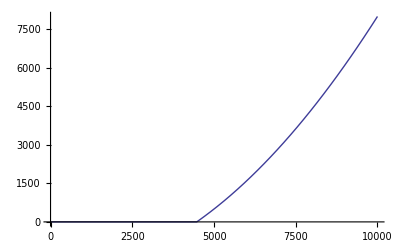

=======================

```mathematica
{{hp2arUnbounded1,hp2mrUnbounded1}} = {y[x],z[x]} /. DSolve[{
	y'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[2]]), 
	z'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[3]])}, (*
	y[hp /. knownBestDistro] == (ar /. knownBestDistro), 
	z[hp /. knownBestDistro] == (mr /. knownBestDistro)}, *)
	{y[x],z[x]}, x];

hp2arUnbounded = Assuming[scale < 1, FullSimplify[hp2arUnbounded1]]
hp2mrUnbounded = Assuming[scale < 1, FullSimplify[hp2mrUnbounded1]]

hp2arCondition = Assuming[{x >= 0, scale < 1, scale ≥ 0}, FullSimplify@Reduce[{hp2arUnbounded >= 0, scale ≥ 0, scale < 1, x >= 0}]]
hp2mrCondition = Assuming[{x >= 0, scale < 1, scale ≥ 0}, FullSimplify@Reduce[{hp2mrUnbounded >= 0, scale ≥ 0, scale < 1, x >= 0}]]

hp2ar[hp_] := Piecewise[{{hp2arUnbounded, hp2arCondition}} /. x -> hp, 0]
hp2mr[hp_] := Piecewise[{{hp2mrUnbounded, hp2mrCondition}} /. x -> hp, 0]
s = 1/2
test1 = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 3000}}, {hp,ar,mr}]]][[2]]
test2 = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 6000}}, {hp,ar,mr}]]][[2]]
Reduce[{hp2ar[hp /. test1] == ar /. test1, hp2mr[hp /. test1] == mr /. test1,
		hp2ar[hp /. test2] == ar /. test2, hp2mr[hp /. test2] == mr /. test2
}, {C[1],C[2]}]
Plot[hp2ar[x] /. {scale -> s, C[1] -> 0, C[2] -> 1/10000}, {x,0,10000}]
"======================="

(*FindInstance[{(hp2mrUnbounded) >= 0, scale ≥ 0, scale < 1, x > 0}, {x,scale}]*)
```

```mathematica
s = 40/100
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 5000}}, {hp,ar,mr}]]]
N@knownBestDistro /. scale -> s
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 10000}}, {hp,ar,mr}]]]
N@knownBestDistro /. scale -> s
{hp2ar[5000.0] /. scale -> s, hp2mr[5000.] /. scale -> s}
{hp2ar[10000.0] /. scale -> s, hp2mr[10000.] /. scale -> s}
```

2/5

{Piecewise[{{-(3125 (-7+5 scale)^2)/(66 (-1+scale)), scale≤1/2}, {(3125 (2+5 scale)^2)/(66 scale), True}}],{hp→Piecewise[{{(500 (-7+5 scale))/(-1+scale), 2 scale≤1}, {(500 (2+5 scale))/scale, True}}],ar→Piecewise[{{250, 2 scale==1}, {(500 (-2+5 scale))/scale, 2 scale>1}, {0, True}}],mr→Piecewise[{{250, 2 scale==1}, {(500 (-3+5 scale))/(-1+scale), 2 scale<1}, {0, True}}]}}

{hp→4166.67,ar→0.,mr→833.333}

{Piecewise[{{-(6250 (6-5 scale)^2)/(33 (-1+scale)), 10 scale==5+√21||2 scale≤1}, {(6250 (1+5 scale)^2)/(33 scale), True}}],{hp→Piecewise[{{(1000 (-6+5 scale))/(-1+scale), 2 scale≤1}, {1000 (5+1/scale), True}}],ar→Piecewise[{{1500, 2 scale==1}, {1000 (5-1/scale), 2 scale>1}, {0, True}}],mr→Piecewise[{{1500, 2 scale==1}, {1000 (5+1/(-1+scale)), 2 scale<1}, {0, True}}]}}

{hp→6666.67,ar→0.,mr→3333.33}

{4444.44,2962.96}

{25277.8,16851.9}

```mathematica
hue[gld_,s_] := {u,hp2ar[u],hp2mr[u]} /. {scale -> s, u -> gld}
s= 0
hp2ar[u]
g
s
Total[hue[30000,s]]
ehp /. {hp -> 15000.0, ar -> 5714, mr -> 12142, scale -> s}
(*
heh[u]:= Module[{constraints}, 
	constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 20000};
	{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]
*)
Show[
	VectorPlot3D[g /. scale -> s, {x,0,30000}, {y,0,30000}, {z,0,30000}, VectorPoints -> Fine, AxesLabel->{hp,ar,mr}, RegionFunction -> Function[{x, y, z}, y ≤ 0]],
	ParametricPlot3D[hue[u,s], {u,0,30000}, AxesLabel->{hp,ar,mr}]
]
```

0

Piecewise[{{Piecewise[{{(-9000000+u^2)/(9000 scale), 1/3≤scale≤2/3}, {250 (3-5/scale)-((-1+scale)^2 u^2)/(1000 scale (-5+3 scale)), 3 scale<1}, {(750 (-2+scale))/scale+(scale u^2)/(1000 (2+3 scale)), True}}], (u<3000&&750000 (-2+3 scale)+scale u^2≥1000 √3 √(3000000+u^2))||(scale>0&&(u≥3000||(u>2500&&2500+scale (-1500+u)≤u)))}, {0, True}}]

{(2000+scale y+z-scale z)/5280,(scale x)/5280,((1-scale) x)/5280}

0

209250

40176.1

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
gHPodd = x /. Solve[{hp2ar[x] + hp2mr[x] + x == h, h ≥ 0, scale ≥ 0, scale < 1, x ≥ 0}, x, 
					Method -> Reduce]

(*gHPodd = Assuming[{scale ≥ 0, scale < 1, h≥ 0}, FullSimplify[gHPodd]]*)

gHPfixed = Piecewise[gHPodd /. ConditionalExpression[xx_, yy_] :> {xx, yy}]

gHP[gold_] := FullSimplify[gHPfixed /. h -> gold]
gAR[h_] := hp2ar[gHP[h]]
gMR[h_] := hp2mr[gHP[h]]
gDistroDef[h_] := {gHP[h],gAR[h],gMR[h]}
```

{ConditionalExpression[-(1000 (-11+10 scale))/(-1+scale)+20 √5 √((22000+11 h-20000 scale-21 h scale+10 h scale^2)/(-1+scale)^2),0<scale<1/2&&(-3500+5000 scale)/(-1+scale)<h<20000],ConditionalExpression[-(1000 (1+10 scale))/scale+20 √5 √((2000+20000 scale+h scale+10 h scale^2)/scale^2),1/2<scale<1&&-5000+h+1500/scale>0&&h<20000],ConditionalExpression[(1000 (-1-9 scale+10 scale^2))/scale+20 √5 √((2000+18000 scale+h scale-19500 scale^2+9 h scale^2+10000 scale^3-10 h scale^3+50000 scale^4)/scale^2),1/2<scale<1&&h>20000],ConditionalExpression[-(1000 (-11 scale+10 scale^2))/(-1+scale)+20 √5 √((60500-209000 scale+11 h scale+310500 scale^2-21 h scale^2-210000 scale^3+10 h scale^3+50000 scale^4)/(-1+scale)^2),0<scale<1/2&&h>20000]}

Piecewise[{{-(1000 (-11+10 scale))/(-1+scale)+20 √5 √((22000+11 h-20000 scale-21 h scale+10 h scale^2)/(-1+scale)^2), 0<scale<1/2&&(-3500+5000 scale)/(-1+scale)<h<20000}, {-(1000 (1+10 scale))/scale+20 √5 √((2000+20000 scale+h scale+10 h scale^2)/scale^2), 1/2<scale<1&&-5000+h+1500/scale>0&&h<20000}, {(1000 (-1-9 scale+10 scale^2))/scale+20 √5 √((2000+18000 scale+h scale-19500 scale^2+9 h scale^2+10000 scale^3-10 h scale^3+50000 scale^4)/scale^2), 1/2<scale<1&&h>20000}, {-(1000 (-11 scale+10 scale^2))/(-1+scale)+20 √5 √((60500-209000 scale+11 h scale+310500 scale^2-21 h scale^2-210000 scale^3+10 h scale^3+50000 scale^4)/(-1+scale)^2), 0<scale<1/2&&h>20000}, {0, True}}]

```mathematica
s=2/5
gold=5000
constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == gold};
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]

N@knownBestDistro /. scale -> s
r = gDistroDef[gold] /. {scale -> s}
N@Total[r]
N@r
```

2/5

5000

{Piecewise[{{-(3125 (-7+5 scale)^2)/(66 (-1+scale)), scale≤1/2}, {(3125 (2+5 scale)^2)/(66 scale), True}}],{hp→Piecewise[{{(500 (-7+5 scale))/(-1+scale), 2 scale≤1}, {(500 (2+5 scale))/scale, True}}],ar→Piecewise[{{250, 2 scale==1}, {(500 (-2+5 scale))/scale, 2 scale>1}, {0, True}}],mr→Piecewise[{{250, 2 scale==1}, {(500 (-3+5 scale))/(-1+scale), 2 scale<1}, {0, True}}]}}

{hp→4166.67,ar→0.,mr→833.333}

{5000/3 (-7+√70),0,2500+2500/21 (-7+√70)^2}

5000.

{2277.67,0.,2722.33}

```mathematica
gDistroDef[10000] /. {scale -> 7/10}
```

Less::nord: Invalid comparison with 15000\ ⅈ/7 attempted.

Less::nord: Invalid comparison with -25000/3 + 15000\ ⅈ/7 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

{Piecewise[{{10000, 10000<(15000 ⅈ)/7}, {2000/49 (-135/2+15 √(555/2)), 10000<-25000/3+(15000 ⅈ)/7}, {0, True}}],2500/7,0}

15000

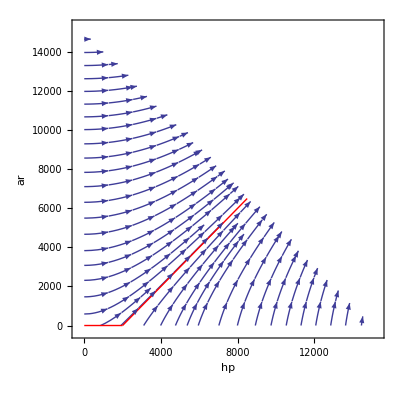

-Graphics3D-

```mathematica
graphLimit = 15000
Block[{scale=0.5},
Show[
  StreamPlot[g, {x, 0, graphLimit}, {y, 0, graphLimit}, 
	RegionFunction -> Function[{x, y, z}, x + y < graphLimit],
	AxesLabel -> {hp,ar}], 

  ParametricPlot[{gHP[u], gAR[u]}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thick]]
]]

display[s_] := Block[{scale=s},Show[
	Plot3D[ehp, {hp,0,graphLimit}, {ar,0,graphLimit}, 
	ColorFunction -> Function[{x, y, z},  ColorData["Thermometer"][z]], 
	AxesLabel-> Automatic,
    RegionFunction -> Function[{x, y, z}, x + y < graphLimit]
],

  ParametricPlot3D[{gHP[u], gAR[u], ehp /. {hp -> gHP[u], ar -> gAR[u]}}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thickness[0.01]]]
]
]
Show[display[1], display[0.5]]
```

```mathematica
gDistroDef[h]
```

{Piecewise[{{h, 0<h<2000}, {(2000+h)/2, h>2000}, {0, True}}],Max[0,-2000+(Piecewise[{{h, 0<h<2000}, {(2000+h)/2, h>2000}, {0, True}}])]}